## Решение задачи штейнера на больших графах

#### Фёдор Курмазов, ПМ-2041

## Задача штейнера на графе.

#### Steiner tree problem in graphs (STP):

Для данного взвешенного неориентированного графа G=(V,E) и множества терминалов T⊆V, требуется найти остовный подграф S графа G наименьшего веса, стягивающий множество T.

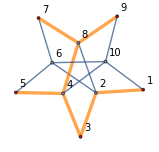

Опр. Для S - допустимого решения задачи, вершиной штейнера называется u ∈ S, u ∉ T.

#### Сложность решения :

Задача разрешимости соответствующая STP является NP-полной.

Оптимизационная версия STP является NP-сложной.

Метрическая STP является APX-полной.

## Структура проекта

#### Организация работы:

```mathematica
-Graphics-             -Graphics-
```

## Реализованные алгоритмы

#### Точные решения :

(DW) Алгоритм Дрейфуса-Вагнера.						O(3^t n+2^t n^2)

#### Приближенные :

(DNH)   2-приближение, алгоритм Коу-Марковского-Бермана. 	     	O(t m log(n))

(DNHA) 2-приближение, алгоритм Мельхорна. 	    			O(m log(n))

#### Жадные :

(SPH) Кратчайшие путей.							O(n m log(n))

(RSPH) Повторные кратчайшие пути.						O(n m log(n))

#### Локальный поиск:

(VI) Вставка вершины штейнера. 						O((n - |S|) m log(n))

(VE) Удаление вершины штейнера. 						O(|S| m log(n))

(PE) Обмен ключевыми путями. 						O(m log(n))

## Алгоритм Дрейфуса-Вагнера

Динамическое программирование.

Задача решается для подмножеств терминалов исходя из решения для подмножеств меньшего размера.

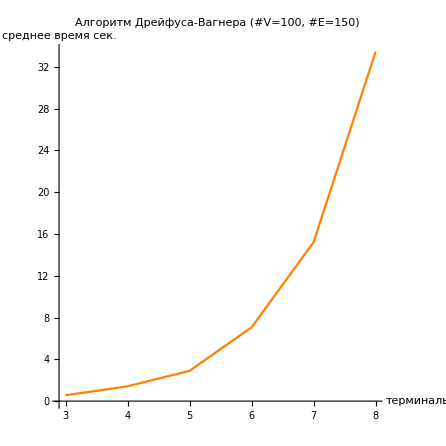

## 2-приближение

#### Алгоритм Коу-Марковского-Бермана:

Построить метрическое замыкание G^* индуцированного графа G[T].

Найти в G^* минимальное остовное дерево.

Найти соответствующие ему пути в G.

Найти минимальное остовное дерево графа из полученных путей и почистить граф от ветвей без терминалов.

#### Время работы:

На 1-ом шаге, для построение метрического замыкания графа, алгоритм вычисляет кратчайшие пути от каждого терминала t∈T до остальных терминалов.

Это занимает O(|T|m log(n)), что плохо при большом количестве терминалов.

#### Алгоритм Мельхорна:

Цель - ускорить первый шаг алгоритма до O(m log n).

Вместо пересчета расстояния от каждой вершины до каждой можно построить диаграмму Вороного.

## Диаграммы Вороного

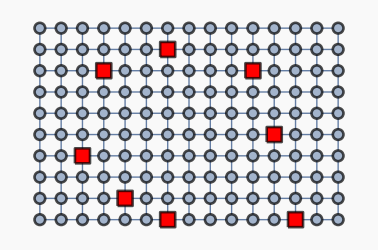
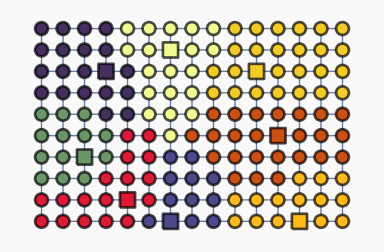
```mathematica
-Graphics-     ->     -Graphics-
```

Множество вершин V разбивается на подмножества относительно заданного множества вершин-центров C ⊆ V так, что вершина u относится к множеству ближайшего центра.

Диаграму можно построить за O(m log n), используя алгоритм Дейкстры.

#### Алгоритм Мельхорна:

По граничным ребрам диаграммы востанавливаются пути между терминалами.В графе этих путей находится минимальное остовное дерево.

Это дерево соответствует дереву в G^* пореберно.

## Локальный поиск.

## Результаты работы

Изучена литература.

Реализованы алгоритмы.

Код структурирован и распределен по пакетам (.wl).

GitHub репозиторий: https://github.com/spefk/wolfram_steiner

## Список источников.

[1] Корте Б. Комбинаторная оптимизация. Теория и Алгоритмы / Бернард Корте, Йенс Фиген ; перевод с англ. М.А. Бабенко ; - М. : МЦНМО ; 2015 - 720 с.

[2] Markowski G. A fast algorithm for steiner trees / G. Markowski, L. Kou, L. Berman ; 1981.

[3] Fuchs B. Speeding up the Dreyfus-Wagner Algorithmfor minimum Steiner trees / B. Fuchs, W. Kern, X. Wang ; 2007

[4] Fomin F.  Computing Optimal Steiner Trees in Polynomial Space / F. Fomin, F. Grandoni, D. Kratsch, D. Lokshtanov, S.Saurabh ; 2012

[5] Dreyfus S.  The Steiner Problem in Graphs / S. Dreyfus, R. Wagner ; 1971

[6] Plesnik J. Heuristics for the Steiner problem in graphs / J. Plesnik ; 1989

[7] Uchoa E. Fast Local Search for Steiner Trees in Graphs / E. Uchoa, R. Werneck  ; 2010

[8] Mehlhorn K. A Faster Approximation Algorithm for the Steiner Tree Problem in Graphs / K. Mehlhorn ; 1988

## init

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
localSearchGifExample = Import["visual//pevive_grid_mehlhorn.gif"];
```

```mathematica
Animate[localSearchGifExample⟦k⟧, {k, 1, Length@localSearchGifExample, 1}, AnimationRate->0.5,AppearanceElements->None]
```

Результатом работы является пакет (.wl) и ноутбук (.nb) с примерами использования.

Основной функционал также распределен по пакетам.

Для контроля версий использовались Git и GitHub.

Для редактирования .wl файлов использовались Wolfram Mathematica и Sublime.

Структура проекта: -Graphics-